```mathematica
g0=9.8 ;
cd=.6;
rho=1.;
area=3.25*10^-3(*Cross sectional area of tennis ball in m^2*);
mass=58*10^-3 (*mass of tennis ball in kg*);
gamma=.5*(1/mass)*rho*area*cd (*drag coefficient*);
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/emmanuelflores/GitHub/Tufts/Spring_2025/Computational_Physics

```mathematica
params={g->9.8, c->gamma, m->mass};
t0=0.00;
tf=0.44;
```

```mathematica
vel = NDSolveValue[{D[v[t], t]==g-c/m v[t]^2,v[0]==0}/.params,v, {t,t0, tf}];
pos = NDSolveValue[{D[v[t],{t,2}]==g-c/m D[v[t],t]^2,v[0]==0, v'[0]==0}/.params, v, {t,t0, tf}];
```

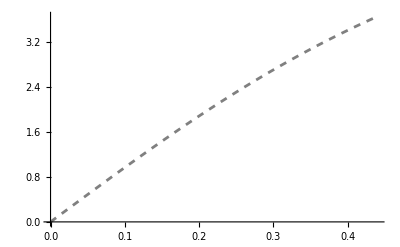

```mathematica
numSolPlot = Plot[vel[x], {x,t0, tf}, PlotStyle->{Dashed, Gray}, PlotRange->All]
```

```mathematica
vTerm=Sqrt[(m g)/c];
```

```mathematica
vAnalytic[t_]:=vTerm Tanh[(g t)/vTerm]
yAnalytic[t_]:=vTerm^2/g Log[Cosh[(g t)/vTerm]]
```

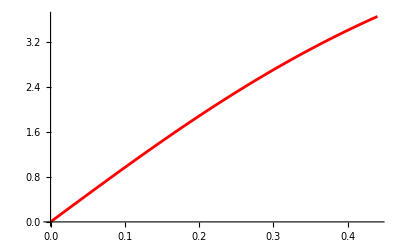

```mathematica
analSolPlot = Plot[vAnalytic[t]/.params,{t,t0, tf}, PlotStyle->Red, PlotRange->All]
```

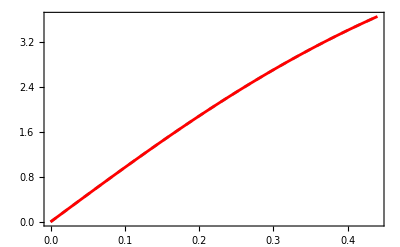

```mathematica
Show[numSolPlot, analSolPlot, Frame->True]
```

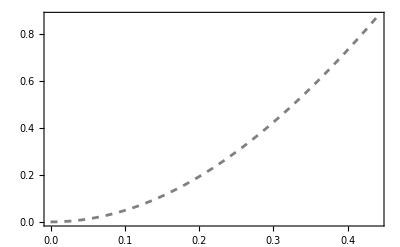

```mathematica
solNumPlot = Plot[pos[t],{t,t0, tf}, PlotStyle->{Dashed, Gray}, Frame->True]
```

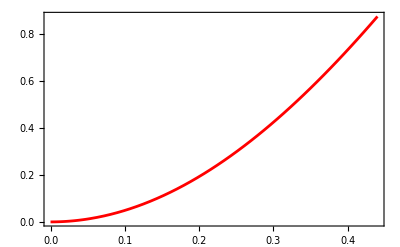

```mathematica
yAnalyticPlot = Plot[yAnalytic[t]/.params,{t,t0, tf}, PlotStyle->Red, Frame->True]
```

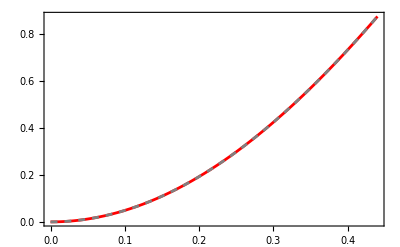

```mathematica
Show[ yAnalyticPlot, solNumPlot]
```

```mathematica
yAnalytic[t]/.params
```

3.45026 Log[Cosh[1.68534 t]]

```mathematica
vAnalytic[t]/.params
```

5.81485 Tanh[1.68534 t]

```mathematica
data = Import["tennis1.txt"];
```

String